```mathematica
(*Authored by Richard Chen
Created: 09/11/2024 3:32PM
Last Updated: 09/11/2024 3:32PM*)
```

## Exponential Function Approach

See how Chi_{n,n}(q) behaves as n grows for q integer

```mathematica
(*Note: the limit for when this expresssion stops running in a reasonable amount of time is degree 34*)
```

```mathematica
Solve[Coefficient[Series[(E^x+E^y-1)^q, {x,0,34},{y,0,34}],x*y,14]==0,q]
```

{{q→0},{q→1},{q→Root2.00Root[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,1]2.},{q→Root3.00Root[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,2]2.9999999999999996},{q→Root4.00Root[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,3]4.000000000063481},{q→Root5.00Root[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,4]4.99999957158495},{q→Root6.00Root[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,5]6.000924575312834},{q→Root6.80Root[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,6]6.797133602498913},{q→Root7.10-0.723 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,7]7.098715542057005},{q→Root7.10+0.723 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,8]7.098715542057005},{q→Root7.46-1.65 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,9]7.456595246227764},{q→Root7.46+1.65 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,10]7.456595246227764},{q→Root7.78-2.69 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,11]7.7824979579994364},{q→Root7.78+2.69 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,12]7.7824979579994364},{q→Root8.08-3.85 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,13]8.08049659231722},{q→Root8.08+3.85 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,14]8.08049659231722},{q→Root8.35-5.14 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,15]8.35441277304023},{q→Root8.35+5.14 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,16]8.35441277304023},{q→Root8.61-6.62 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,17]8.607964226045073},{q→Root8.61+6.62 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,18]8.607964226045073},{q→Root8.84-8.31 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,19]8.844916182319468},{q→Root8.84+8.31 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,20]8.844916182319468},{q→Root9.07-10.3 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,21]9.069728177701375},{q→Root9.07+10.3 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,22]9.069728177701375},{q→Root9.29-12.7 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,23]9.28894698585688},{q→Root9.29+12.7 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,24]9.28894698585688},{q→Root9.52-15.9 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,25]9.516697036979775},{q→Root9.52+15.9 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,26]9.516697036979775}}

Look at Chi_ {n, n} (2)

```mathematica
chiTwo:=Table[Factorial[n]^2*Coefficient[Series[(E^x+E^y-1)^2, {x,0,n},{y,0,n}],x*y,n],{n,0,10}]
```

Look at Chi_ {n, n} (3)

```mathematica
chiThree:=Table[Factorial[n]^2*Coefficient[Series[(E^x+E^y-1)^3, {x,0,n},{y,0,n}],x*y,n],{n,0,10}]
```

Look at Chi_ {n, n} (4)

```mathematica
chiFour:=Table[Factorial[n]^2*Coefficient[Series[(E^x + E^y - 1)^4, {x, 0, n}, {y, 0, n}], x*y, n], {n, 0, 10}]
```

Look at Chi_ {n, n} (5)

```mathematica
chiFive:=Table[Factorial[n]^2*Coefficient[Series[(E^x+E^y-1)^5, {x,0,n},{y,0,n}],x*y,n],{n,0,10}]
```

```mathematica
chiList:={chiTwo,chiThree,chiFour,chiFive}
```

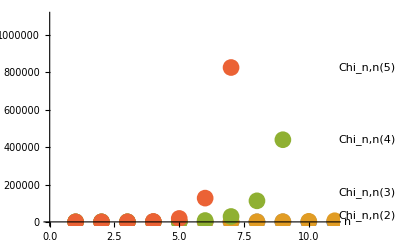

```mathematica
ListPlot[Table[Labeled[chiList[[j-1]],StringJoin[{"Chi_n,n(", ToString[j],")"}]],{j,2,5}],PlotStyle->PointSize[0.03],AxesLabel->{"n",""}]
```

```mathematica
Solve[Coefficient[Series[(E^x+E^y+E^z-1)^q, {x,0,10},{y,0,10},{z,0,10}],x*y,14]==0,q]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

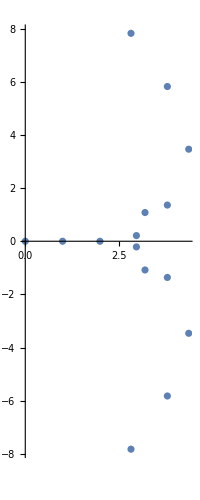

```mathematica
ComplexListPlot[q/.N[Solve[Coefficient[Series[(E^x+E^y+E^z-1)^q, {x,0,5},{y,0,5},{z,0,5}],x*y*z,5]==0,q]]]
```

```mathematica
tripartiteList=Table[(q/n)/.Solve[Coefficient[Series[(E^x+E^y+E^z-2)^q, {x,0,n},{y,0,n},{z,0,n}],x*y*z,n]==0,q],{n,2,9}]
```

{{0,1/2,1,1/2 Root2.55Root[-32+29 #1-9 #1^2+#1^3&,1]2.546602348483595,1/2 Root3.23-1.47 ⅈRoot[-32+29 #1-9 #1^2+#1^3&,2]3.2266988257582017,1/2 Root3.23+1.47 ⅈRoot[-32+29 #1-9 #1^2+#1^3&,3]3.2266988257582017},{0,1/3,2/3,1/3 Root3.09Root[5914-8112 #1+4639 #1^2-1425 #1^3+250 #1^4-24 #1^5+#1^6&,1]3.0922054607707214,1/3 Root3.32Root[5914-8112 #1+4639 #1^2-1425 #1^3+250 #1^4-24 #1^5+#1^6&,2]3.3224925838208916,1/3 Root4.02-1.26 ⅈRoot[5914-8112 #1+4639 #1^2-1425 #1^3+250 #1^4-24 #1^5+#1^6&,3]4.021436806758125,1/3 Root4.02+1.26 ⅈRoot[5914-8112 #1+4639 #1^2-1425 #1^3+250 #1^4-24 #1^5+#1^6&,4]4.021436806758125,1/3 Root4.77-3.11 ⅈRoot[5914-8112 #1+4639 #1^2-1425 #1^3+250 #1^4-24 #1^5+#1^6&,5]4.771214170946309,1/3 Root4.77+3.11 ⅈRoot[5914-8112 #1+4639 #1^2-1425 #1^3+250 #1^4-24 #1^5+#1^6&,6]4.771214170946309},{0,1/4,1/2,1/4 Root3.00Root[-3238322+5466914 #1-4070160 #1^2+1760205 #1^3-489153 #1^4+90963 #1^5-11373 #1^6+927 #1^7-45 #1^8+#1^9&,1]2.9997022927638812,1/4 Root4.19-0.0286 ⅈRoot[-3238322+5466914 #1-4070160 #1^2+1760205 #1^3-489153 #1^4+90963 #1^5-11373 #1^6+927 #1^7-45 #1^8+#1^9&,2]4.185260768829609,1/4 Root4.19+0.0286 ⅈRoot[-3238322+5466914 #1-4070160 #1^2+1760205 #1^3-489153 #1^4+90963 #1^5-11373 #1^6+927 #1^7-45 #1^8+#1^9&,3]4.185260768829609,1/4 Root4.88-1.21 ⅈRoot[-3238322+5466914 #1-4070160 #1^2+1760205 #1^3-489153 #1^4+90963 #1^5-11373 #1^6+927 #1^7-45 #1^8+#1^9&,4]4.878859372992789,1/4 Root4.88+1.21 ⅈRoot[-3238322+5466914 #1-4070160 #1^2+1760205 #1^3-489153 #1^4+90963 #1^5-11373 #1^6+927 #1^7-45 #1^8+#1^9&,5]4.878859372992789,1/4 Root5.58-2.69 ⅈRoot[-3238322+5466914 #1-4070160 #1^2+1760205 #1^3-489153 #1^4+90963 #1^5-11373 #1^6+927 #1^7-45 #1^8+#1^9&,6]5.582138154172259,1/4 Root5.58+2.69 ⅈRoot[-3238322+5466914 #1-4070160 #1^2+1760205 #1^3-489153 #1^4+90963 #1^5-11373 #1^6+927 #1^7-45 #1^8+#1^9&,7]5.582138154172259,1/4 Root6.35-4.81 ⅈRoot[-3238322+5466914 #1-4070160 #1^2+1760205 #1^3-489153 #1^4+90963 #1^5-11373 #1^6+927 #1^7-45 #1^8+#1^9&,8]6.353890557624891,1/4 Root6.35+4.81 ⅈRoot[-3238322+5466914 #1-4070160 #1^2+1760205 #1^3-489153 #1^4+90963 #1^5-11373 #1^6+927 #1^7-45 #1^8+#1^9&,9]6.353890557624891},{0,1/5,2/5,1/5 Root3.00Root[3919435246-7558129896 #1+6602632558 #1^2-3464018440 #1^3+1218751181 #1^4-303743805 #1^5+55137642 #1^6-7367052 #1^7+721356 #1^8-50660 #1^9+2432 #1^10-72 #1^11+#1^12&,1]3.0000005380771047,1/5 Root4.00Root[3919435246-7558129896 #1+6602632558 #1^2-3464018440 #1^3+1218751181 #1^4-303743805 #1^5+55137642 #1^6-7367052 #1^7+721356 #1^8-50660 #1^9+2432 #1^10-72 #1^11+#1^12&,2]3.9996358425695413,1/5 Root5.15-0.123 ⅈRoot[3919435246-7558129896 #1+6602632558 #1^2-3464018440 #1^3+1218751181 #1^4-303743805 #1^5+55137642 #1^6-7367052 #1^7+721356 #1^8-50660 #1^9+2432 #1^10-72 #1^11+#1^12&,3]5.1533248382563945,1/5 Root5.15+0.123 ⅈRoot[3919435246-7558129896 #1+6602632558 #1^2-3464018440 #1^3+1218751181 #1^4-303743805 #1^5+55137642 #1^6-7367052 #1^7+721356 #1^8-50660 #1^9+2432 #1^10-72 #1^11+#1^12&,4]5.1533248382563945,1/5 Root5.80-1.22 ⅈRoot[3919435246-7558129896 #1+6602632558 #1^2-3464018440 #1^3+1218751181 #1^4-303743805 #1^5+55137642 #1^6-7367052 #1^7+721356 #1^8-50660 #1^9+2432 #1^10-72 #1^11+#1^12&,5]5.800216902205014,1/5 Root5.80+1.22 ⅈRoot[3919435246-7558129896 #1+6602632558 #1^2-3464018440 #1^3+1218751181 #1^4-303743805 #1^5+55137642 #1^6-7367052 #1^7+721356 #1^8-50660 #1^9+2432 #1^10-72 #1^11+#1^12&,6]5.800216902205014,1/5 Root6.45-2.51 ⅈRoot[3919435246-7558129896 #1+6602632558 #1^2-3464018440 #1^3+1218751181 #1^4-303743805 #1^5+55137642 #1^6-7367052 #1^7+721356 #1^8-50660 #1^9+2432 #1^10-72 #1^11+#1^12&,7]6.447415849686452,1/5 Root6.45+2.51 ⅈRoot[3919435246-7558129896 #1+6602632558 #1^2-3464018440 #1^3+1218751181 #1^4-303743805 #1^5+55137642 #1^6-7367052 #1^7+721356 #1^8-50660 #1^9+2432 #1^10-72 #1^11+#1^12&,8]6.447415849686452,1/5 Root7.15-4.21 ⅈRoot[3919435246-7558129896 #1+6602632558 #1^2-3464018440 #1^3+1218751181 #1^4-303743805 #1^5+55137642 #1^6-7367052 #1^7+721356 #1^8-50660 #1^9+2432 #1^10-72 #1^11+#1^12&,9]7.146076294013563,1/5 Root7.15+4.21 ⅈRoot[3919435246-7558129896 #1+6602632558 #1^2-3464018440 #1^3+1218751181 #1^4-303743805 #1^5+55137642 #1^6-7367052 #1^7+721356 #1^8-50660 #1^9+2432 #1^10-72 #1^11+#1^12&,10]7.146076294013563,1/5 Root7.95-6.56 ⅈRoot[3919435246-7558129896 #1+6602632558 #1^2-3464018440 #1^3+1218751181 #1^4-303743805 #1^5+55137642 #1^6-7367052 #1^7+721356 #1^8-50660 #1^9+2432 #1^10-72 #1^11+#1^12&,11]7.953147925131662,1/5 Root7.95+6.56 ⅈRoot[3919435246-7558129896 #1+6602632558 #1^2-3464018440 #1^3+1218751181 #1^4-303743805 #1^5+55137642 #1^6-7367052 #1^7+721356 #1^8-50660 #1^9+2432 #1^10-72 #1^11+#1^12&,12]7.953147925131662},{0,1/6,1/3,1/6 Root3.00Root[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,1]2.999999999558379,1/6 Root4.00Root[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,2]4.000000765161627,1/6 Root5.00Root[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,3]4.99953182588768,1/6 Root6.12-0.186 ⅈRoot[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,4]6.118043313905032,1/6 Root6.12+0.186 ⅈRoot[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,5]6.118043313905032,1/6 Root6.75-1.22 ⅈRoot[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,6]6.745557060071967,1/6 Root6.75+1.22 ⅈRoot[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,7]6.745557060071967,1/6 Root7.35-2.42 ⅈRoot[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,8]7.349039300822816,1/6 Root7.35+2.42 ⅈRoot[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,9]7.349039300822816,1/6 Root8.01-3.91 ⅈRoot[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,10]8.006486058319744,1/6 Root8.01+3.91 ⅈRoot[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,11]8.006486058319744,1/6 Root8.72-5.79 ⅈRoot[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,12]8.71863704591706,1/6 Root8.72+5.79 ⅈRoot[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,13]8.71863704591706,1/6 Root9.56-8.35 ⅈRoot[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,14]9.562470927876518,1/6 Root9.56+8.35 ⅈRoot[-8870157730922+18822020397458 #1-18382653936120 #1^2+10984638284000 #1^3-4500530139510 #1^4+1341908617811 #1^5-301416367413 #1^6+52042132205 #1^7-6978495645 #1^8+728350210 #1^9-58822086 #1^10+3618940 #1^11-164640 #1^12+5245 #1^13-105 #1^14+#1^15&,15]9.562470927876518},{0,1/7,2/7,1/7 Root3.00Root[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,1]3.0000000000001945,1/7 Root4.00Root[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,2]3.9999999991830824,1/7 Root5.00Root[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,3]5.000001198827346,1/7 Root6.00Root[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,4]5.999278423054849,1/7 Root7.09-0.230 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,5]7.085148348743404,1/7 Root7.09+0.230 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,6]7.085148348743404,1/7 Root7.69-1.23 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,7]7.6938341243344786,1/7 Root7.69+1.23 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,8]7.6938341243344786,1/7 Root8.28-2.38 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,9]8.276619283626871,1/7 Root8.28+2.38 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,10]8.276619283626871,1/7 Root8.90-3.74 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,11]8.899534236024515,1/7 Root8.90+3.74 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,12]8.899534236024515,1/7 Root9.57-5.39 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,13]9.567070996808518,1/7 Root9.57+5.39 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,14]9.567070996808518,1/7 Root10.3-7.43 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,15]10.299341670857022,1/7 Root10.3+7.43 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,16]10.299341670857022,1/7 Root11.2-10.2 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,17]11.178811397238775,1/7 Root11.2+10.2 ⅈRoot[33670778886322894-76907162681193924 #1+81709646676815584 #1^2-53752585352666780 #1^3+24578597729001174 #1^4-8309495240726988 #1^5+2156131022405739 #1^6-439765291894005 #1^7+71588392330458 #1^8-9386034241618 #1^9+995151439681 #1^10-85265769663 #1^11+5870524164 #1^12-320985462 #1^13+13659075 #1^14-437457 #1^15+9954 #1^16-144 #1^17+#1^18&,18]11.178811397238775},{0,1/8,1/4,1/8 Root3.00Root[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,1]3.,1/8 Root4.00Root[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,2]4.000000000000504,1/8 Root5.00Root[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,3]4.999999998288155,1/8 Root6.00Root[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,4]6.000002304021592,1/8 Root7.00Root[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,5]6.998968710511939,1/8 Root8.05-0.264 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,6]8.052696502129972,1/8 Root8.05+0.264 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,7]8.052696502129972,1/8 Root8.64-1.24 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,8]8.644370457049458,1/8 Root8.64+1.24 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,9]8.644370457049458,1/8 Root9.22-2.36 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,10]9.216776367350155,1/8 Root9.22+2.36 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,11]9.216776367350155,1/8 Root9.82-3.64 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,12]9.815271149445957,1/8 Root9.82+3.64 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,13]9.815271149445957,1/8 Root10.5-5.14 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,14]10.451459219153874,1/8 Root10.5+5.14 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,15]10.451459219153874,1/8 Root11.1-6.92 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,16]11.132477371884809,1/8 Root11.1+6.92 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,17]11.132477371884809,1/8 Root11.9-9.10 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,18]11.88703786196115,1/8 Root11.9+9.10 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,19]11.88703786196115,1/8 Root12.8-12.0 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,20]12.80042556461353,1/8 Root12.8+12.0 ⅈRoot[-198619290419132373242+481372457366523053990 #1-546792544420406455290 #1^2+387804337745934697126 #1^3-192963876527930526438 #1^4+71737083704768068846 #1^5-20713737391969052144 #1^6+4766005075994397837 #1^7-889277901788054481 #1^8+136176384671399807 #1^9-17247954524108049 #1^10+1814919276131675 #1^11-158870030814845 #1^12+11549074291195 #1^13-693695228925 #1^14+34113721719 #1^15-1353581985 #1^16+42366639 #1^17-1009505 #1^18+17255 #1^19-189 #1^20+#1^21&,21]12.80042556461353},{0,1/9,2/9,1/9 Root3.00Root[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,1]3.,1/9 Root4.00Root[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,2]4.,1/9 Root5.00Root[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,3]5.0000000000015055,1/9 Root6.00Root[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,4]5.999999995564048,1/9 Root7.00Root[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,5]7.000003704989317,1/9 Root8.00Root[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,6]7.998586602401943,1/9 Root9.02-0.294 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,7]9.019550851048987,1/9 Root9.02+0.294 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,8]9.019550851048987,1/9 Root9.60-1.25 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,9]9.597815514416775,1/9 Root9.60+1.25 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,10]9.597815514416775,1/9 Root10.2-2.34 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,11]10.162361277835966,1/9 Root10.2+2.34 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,12]10.162361277835966,1/9 Root10.7-3.57 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,13]10.7458499760409,1/9 Root10.7+3.57 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,14]10.7458499760409,1/9 Root11.4-4.97 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,15]11.358199377906825,1/9 Root11.4+4.97 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,16]11.358199377906825,1/9 Root12.0-6.59 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,17]12.006696457356695,1/9 Root12.0+6.59 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,18]12.006696457356695,1/9 Root12.7-8.49 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,19]12.703370935433272,1/9 Root12.7+8.49 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,20]12.703370935433272,1/9 Root13.5-10.8 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,21]13.480664948593276,1/9 Root13.5+10.8 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,22]13.480664948593276,1/9 Root14.4-13.8 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,23]14.426195509888895,1/9 Root14.4+13.8 ⅈRoot[1720407440750704335900766-4380167804069152206301152 #1+5256742653959015752459618 #1^2-3963568349136963436477440 #1^3+2110926394806957228236092 #1^4-846260868252110906050848 #1^5+265691143351178203805020 #1^6-67089251932078981896048 #1^7+13882144886696773680385 #1^8-2385718974242086028133 #1^9+«9»+94767099467812 #1^16-4233215583924 #1^17+156727697896 #1^18-4731954192 #1^19+113744848 #1^20-2098128 #1^21+27952 #1^22-240 #1^23+#1^24&,24]14.426195509888895}}

```mathematica
bipartiteList=Table[(q/n)/.Solve[Coefficient[Series[(E^x+E^y-1)^q, {x,0,n},{y,0,n}],x*y,n]==0,q],{n,2,14}]
```

```mathematica
fourpartiteList=Table[(q/n)/.Solve[Coefficient[Series[(E^x+E^y+E^z+E^w-3)^q, {x,0,n},{y,0,n},{z,0,n},{w,0,n}],x*y*z*w,n]==0,q],{n,2,5}]
```

{{0,1/2,1,3/2,1/2 Root3.96-0.446 ⅈRoot[465-392 #1+125 #1^2-18 #1^3+#1^4&,1]3.9578873762421543,1/2 Root3.96+0.446 ⅈRoot[465-392 #1+125 #1^2-18 #1^3+#1^4&,2]3.9578873762421543,1/2 Root5.04-1.97 ⅈRoot[465-392 #1+125 #1^2-18 #1^3+#1^4&,3]5.04211262375791,1/2 Root5.04+1.97 ⅈRoot[465-392 #1+125 #1^2-18 #1^3+#1^4&,4]5.04211262375791},{0,1/3,2/3,1,1/3 Root4.00Root[2082993-2693016 #1+1516699 #1^2-487128 #1^3+97834 #1^4-12618 #1^5+1024 #1^6-48 #1^7+#1^8&,1]4.001206048571971,1/3 Root4.90Root[2082993-2693016 #1+1516699 #1^2-487128 #1^3+97834 #1^4-12618 #1^5+1024 #1^6-48 #1^7+#1^8&,2]4.904357358234292,1/3 Root5.59-0.774 ⅈRoot[2082993-2693016 #1+1516699 #1^2-487128 #1^3+97834 #1^4-12618 #1^5+1024 #1^6-48 #1^7+#1^8&,3]5.586180474766607,1/3 Root5.59+0.774 ⅈRoot[2082993-2693016 #1+1516699 #1^2-487128 #1^3+97834 #1^4-12618 #1^5+1024 #1^6-48 #1^7+#1^8&,4]5.586180474766607,1/3 Root6.44-2.07 ⅈRoot[2082993-2693016 #1+1516699 #1^2-487128 #1^3+97834 #1^4-12618 #1^5+1024 #1^6-48 #1^7+#1^8&,5]6.437216294880564,1/3 Root6.44+2.07 ⅈRoot[2082993-2693016 #1+1516699 #1^2-487128 #1^3+97834 #1^4-12618 #1^5+1024 #1^6-48 #1^7+#1^8&,6]6.437216294880564,1/3 Root7.52-4.05 ⅈRoot[2082993-2693016 #1+1516699 #1^2-487128 #1^3+97834 #1^4-12618 #1^5+1024 #1^6-48 #1^7+#1^8&,7]7.523821526952863,1/3 Root7.52+4.05 ⅈRoot[2082993-2693016 #1+1516699 #1^2-487128 #1^3+97834 #1^4-12618 #1^5+1024 #1^6-48 #1^7+#1^8&,8]7.523821526952863},{0,1/4,1/2,3/4,1/4 Root4.00Root[38766040209-62102135976 #1+45203485953 #1^2-19797448988 #1^3+5819052293 #1^4-1211173992 #1^5+183344253 #1^6-20373450 #1^7+1652445 #1^8-95598 #1^9+3753 #1^10-90 #1^11+#1^12&,1]4.000000262572167,1/4 Root5.00Root[38766040209-62102135976 #1+45203485953 #1^2-19797448988 #1^3+5819052293 #1^4-1211173992 #1^5+183344253 #1^6-20373450 #1^7+1652445 #1^8-95598 #1^9+3753 #1^10-90 #1^11+#1^12&,2]4.999895407630629,1/4 Root6.02Root[38766040209-62102135976 #1+45203485953 #1^2-19797448988 #1^3+5819052293 #1^4-1211173992 #1^5+183344253 #1^6-20373450 #1^7+1652445 #1^8-95598 #1^9+3753 #1^10-90 #1^11+#1^12&,3]6.017655652459538,1/4 Root6.64Root[38766040209-62102135976 #1+45203485953 #1^2-19797448988 #1^3+5819052293 #1^4-1211173992 #1^5+183344253 #1^6-20373450 #1^7+1652445 #1^8-95598 #1^9+3753 #1^10-90 #1^11+#1^12&,4]6.64226881145989,1/4 Root7.21-1.03 ⅈRoot[38766040209-62102135976 #1+45203485953 #1^2-19797448988 #1^3+5819052293 #1^4-1211173992 #1^5+183344253 #1^6-20373450 #1^7+1652445 #1^8-95598 #1^9+3753 #1^10-90 #1^11+#1^12&,5]7.211443461407188,1/4 Root7.21+1.03 ⅈRoot[38766040209-62102135976 #1+45203485953 #1^2-19797448988 #1^3+5819052293 #1^4-1211173992 #1^5+183344253 #1^6-20373450 #1^7+1652445 #1^8-95598 #1^9+3753 #1^10-90 #1^11+#1^12&,6]7.211443461407188,1/4 Root7.99-2.30 ⅈRoot[38766040209-62102135976 #1+45203485953 #1^2-19797448988 #1^3+5819052293 #1^4-1211173992 #1^5+183344253 #1^6-20373450 #1^7+1652445 #1^8-95598 #1^9+3753 #1^10-90 #1^11+#1^12&,7]7.985212538318439,1/4 Root7.99+2.30 ⅈRoot[38766040209-62102135976 #1+45203485953 #1^2-19797448988 #1^3+5819052293 #1^4-1211173992 #1^5+183344253 #1^6-20373450 #1^7+1652445 #1^8-95598 #1^9+3753 #1^10-90 #1^11+#1^12&,8]7.985212538318439,1/4 Root8.92-3.92 ⅈRoot[38766040209-62102135976 #1+45203485953 #1^2-19797448988 #1^3+5819052293 #1^4-1211173992 #1^5+183344253 #1^6-20373450 #1^7+1652445 #1^8-95598 #1^9+3753 #1^10-90 #1^11+#1^12&,9]8.916193358789544,1/4 Root8.92+3.92 ⅈRoot[38766040209-62102135976 #1+45203485953 #1^2-19797448988 #1^3+5819052293 #1^4-1211173992 #1^5+183344253 #1^6-20373450 #1^7+1652445 #1^8-95598 #1^9+3753 #1^10-90 #1^11+#1^12&,10]8.916193358789544,1/4 Root10.1-6.20 ⅈRoot[38766040209-62102135976 #1+45203485953 #1^2-19797448988 #1^3+5819052293 #1^4-1211173992 #1^5+183344253 #1^6-20373450 #1^7+1652445 #1^8-95598 #1^9+3753 #1^10-90 #1^11+#1^12&,11]10.057240584567328,1/4 Root10.1+6.20 ⅈRoot[38766040209-62102135976 #1+45203485953 #1^2-19797448988 #1^3+5819052293 #1^4-1211173992 #1^5+183344253 #1^6-20373450 #1^7+1652445 #1^8-95598 #1^9+3753 #1^10-90 #1^11+#1^12&,12]10.057240584567328},{0,1/5,2/5,3/5,1/5 Root4.00Root[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,1]4.000000000013976,1/5 Root5.00Root[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,2]4.999999984336338,1/5 Root6.00Root[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,3]6.000006829821946,1/5 Root7.00Root[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,4]6.998522296520967,1/5 Root8.11-0.243 ⅈRoot[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,5]8.10726684334705,1/5 Root8.11+0.243 ⅈRoot[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,6]8.10726684334705,1/5 Root8.84-1.30 ⅈRoot[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,7]8.841907373507304,1/5 Root8.84+1.30 ⅈRoot[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,8]8.841907373507304,1/5 Root9.59-2.54 ⅈRoot[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,9]9.594244374856258,1/5 Root9.59+2.54 ⅈRoot[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,10]9.594244374856258,1/5 Root10.4-4.02 ⅈRoot[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,11]10.431496050360465,1/5 Root10.4+4.02 ⅈRoot[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,12]10.431496050360465,1/5 Root11.4-5.87 ⅈRoot[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,13]11.410835230382668,1/5 Root11.4+5.87 ⅈRoot[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,14]11.410835230382668,1/5 Root12.6-8.39 ⅈRoot[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,15]12.614985420700197,1/5 Root12.6+8.39 ⅈRoot[2051987079085521-3771058209902352 #1+3213806812316727 #1^2-1687867261841940 #1^3+612121195805776 #1^4-162725805082020 #1^5+32838937959184 #1^6-5137646301880 #1^7+630494205566 #1^8-60968986770 #1^9+4636059540 #1^10-274652664 #1^11+12444876 #1^12-417560 #1^13+9800 #1^14-144 #1^15+#1^16&,16]12.614985420700197}}

```mathematica
fivepartiteList=Table[(q/n)/.Solve[Coefficient[Series[(E^x+E^y+E^z+E^w+E^v-4)^q, {x,0,n},{y,0,n},{z,0,n},{w,0,n},{v,0,n}],x*y*z*w*v,n]==0,q],{n,2,4}]
```

{{0,1/2,1,3/2,2,1/2 Root4.91Root[-8544+6909 #1-2240 #1^2+365 #1^3-30 #1^4+#1^5&,1]4.905297575553567,1/2 Root5.65-0.836 ⅈRoot[-8544+6909 #1-2240 #1^2+365 #1^3-30 #1^4+#1^5&,2]5.646488674917115,1/2 Root5.65+0.836 ⅈRoot[-8544+6909 #1-2240 #1^2+365 #1^3-30 #1^4+#1^5&,3]5.646488674917115,1/2 Root6.90-2.42 ⅈRoot[-8544+6909 #1-2240 #1^2+365 #1^3-30 #1^4+#1^5&,4]6.900862537306051,1/2 Root6.90+2.42 ⅈRoot[-8544+6909 #1-2240 #1^2+365 #1^3-30 #1^4+#1^5&,5]6.900862537306051},{0,1/3,2/3,1,4/3,1/3 Root5.00Root[1179189316-1473030668 #1+823636361 #1^2-271753660 #1^3+58661655 #1^4-8667532 #1^5+888978 #1^6-62590 #1^7+2900 #1^8-80 #1^9+#1^10&,1]5.000015611584701,1/3 Root6.00Root[1179189316-1473030668 #1+823636361 #1^2-271753660 #1^3+58661655 #1^4-8667532 #1^5+888978 #1^6-62590 #1^7+2900 #1^8-80 #1^9+#1^10&,2]5.9972892839894065,1/3 Root7.13-0.266 ⅈRoot[1179189316-1473030668 #1+823636361 #1^2-271753660 #1^3+58661655 #1^4-8667532 #1^5+888978 #1^6-62590 #1^7+2900 #1^8-80 #1^9+#1^10&,3]7.126430331354209,1/3 Root7.13+0.266 ⅈRoot[1179189316-1473030668 #1+823636361 #1^2-271753660 #1^3+58661655 #1^4-8667532 #1^5+888978 #1^6-62590 #1^7+2900 #1^8-80 #1^9+#1^10&,4]7.126430331354209,1/3 Root8.03-1.40 ⅈRoot[1179189316-1473030668 #1+823636361 #1^2-271753660 #1^3+58661655 #1^4-8667532 #1^5+888978 #1^6-62590 #1^7+2900 #1^8-80 #1^9+#1^10&,5]8.025515725350404,1/3 Root8.03+1.40 ⅈRoot[1179189316-1473030668 #1+823636361 #1^2-271753660 #1^3+58661655 #1^4-8667532 #1^5+888978 #1^6-62590 #1^7+2900 #1^8-80 #1^9+#1^10&,6]8.025515725350404,1/3 Root9.01-2.82 ⅈRoot[1179189316-1473030668 #1+823636361 #1^2-271753660 #1^3+58661655 #1^4-8667532 #1^5+888978 #1^6-62590 #1^7+2900 #1^8-80 #1^9+#1^10&,7]9.012877595468114,1/3 Root9.01+2.82 ⅈRoot[1179189316-1473030668 #1+823636361 #1^2-271753660 #1^3+58661655 #1^4-8667532 #1^5+888978 #1^6-62590 #1^7+2900 #1^8-80 #1^9+#1^10&,8]9.012877595468114,1/3 Root10.3-4.87 ⅈRoot[1179189316-1473030668 #1+823636361 #1^2-271753660 #1^3+58661655 #1^4-8667532 #1^5+888978 #1^6-62590 #1^7+2900 #1^8-80 #1^9+#1^10&,9]10.33652390068118,1/3 Root10.3+4.87 ⅈRoot[1179189316-1473030668 #1+823636361 #1^2-271753660 #1^3+58661655 #1^4-8667532 #1^5+888978 #1^6-62590 #1^7+2900 #1^8-80 #1^9+#1^10&,10]10.33652390068118},{0,1/4,1/2,3/4,1,1/4 Root5.00Root[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,1]4.999999999888689,1/4 Root6.00Root[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,2]6.0000000664270905,1/4 Root7.00Root[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,3]6.999983837586475,1/4 Root8.00Root[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,4]8.002119049074388,1/4 Root8.89Root[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,5]8.894235392138281,1/4 Root9.57-0.764 ⅈRoot[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,6]9.572567750262854,1/4 Root9.57+0.764 ⅈRoot[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,7]9.572567750262854,1/4 Root10.4-1.93 ⅈRoot[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,8]10.39402045244273,1/4 Root10.4+1.93 ⅈRoot[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,9]10.39402045244273,1/4 Root11.3-3.32 ⅈRoot[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,10]11.323581689456109,1/4 Root11.3+3.32 ⅈRoot[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,11]11.323581689456109,1/4 Root12.4-5.03 ⅈRoot[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,12]12.427312266962002,1/4 Root12.4+5.03 ⅈRoot[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,13]12.427312266962002,1/4 Root13.8-7.39 ⅈRoot[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,14]13.834348638237989,1/4 Root13.8+7.39 ⅈRoot[-948615984528564+1474062658281008 #1-1060302323106104 #1^2+468679973818309 #1^3-142483284809680 #1^4+31581602130837 #1^5-5276668417412 #1^6+677281139933 #1^7-67389585840 #1^8+5202572925 #1^9-309379414 #1^10+13930677 #1^11-460250 #1^12+10545 #1^13-150 #1^14+#1^15&,15]13.834348638237989}}

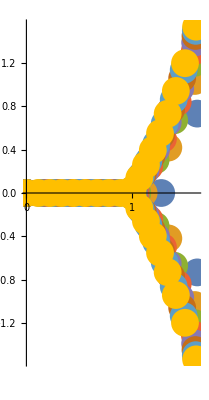

```mathematica
tripartite=ComplexListPlot[Table[(q/n)/.Solve[Coefficient[Series[(E^x+E^y+E^z-2)^q, {x,0,n},{y,0,n},{z,0,n}],x*y*z,n]==0,q],{n,2,9}],PlotStyle->PointSize[0.05]]
```

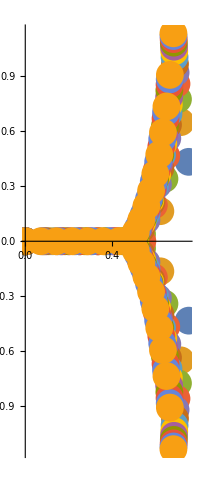

```mathematica
bipartite=ComplexListPlot[Table[(q/n)/.Solve[Coefficient[Series[(E^x+E^y-1)^q, {x,0,n},{y,0,n}],x*y,n]==0,q],{n,2,14}],PlotStyle->PointSize[0.05]]
```

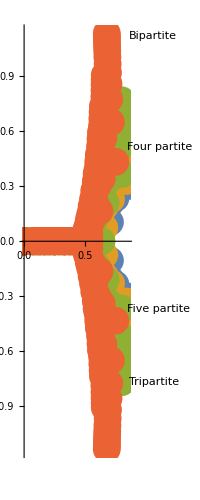

```mathematica
ComplexListPlot[MapThread[Labeled,{Flatten/@{fivepartiteList/4,fourpartiteList/3,tripartiteList/2, bipartiteList},{"Five partite", "Four partite", "Tripartite", "Bipartite"}}],PlotStyle->PointSize[0.05],PlotStyle->{Red, Green,Blue}]
```

```mathematica
ComplexListPlot[MapThread[Labeled,Flatten/@{fivepartiteList/4,fourpartiteList/3,tripartiteList/2, bipartiteList},{"Five partite", "Four partite", "Tripartite", "Bipartite"}],PlotStyle->PointSize[0.05],PlotStyle->{Red, Green,Blue,Orange}]
```

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[Labeled,{{0,1/8,1/4,3/8,«4»,1/8 Root[-8544+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Power[«2»]&,4,0],1/8 Root[-8544+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Power[«2»]&,5,0],«35»},{0,1/6,1/3,1/2,1/6 «1»,«1»,«1»,1/6 Root[465+«4»&,4,0],0,1/9,«46»},«1»,{0,1/2,«8»,«198»}},{Five partite,Four partite,Tripartite,Bipartite}].

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[Labeled,{{0,0.125,0.25,«6»,0.8626078171632629+0.3019778621978 ⅈ,«35»},{0,0.1666666666666667,«8»,«46»},{0,«9»,«122»},{0,0.5,«8»,«198»}},{Five partite,Four partite,Tripartite,Bipartite}].

MapThread::intnm: Non-negative machine-sized integer expected at position 3 in MapThread[Labeled,{{0.,0.125,0.25,0.375,0.5,0.613162,0.705811-0.104546 ⅈ,0.705811+0.104546 ⅈ,0.862608-0.301978 ⅈ,0.862608+0.301978 ⅈ,«35»},«2»,{0.,«9»,«198»}},{Five partite,Four partite,Tripartite,Bipartite}].

General::stop: Further output of MapThread::intnm will be suppressed during this calculation.

ComplexListPlot::ldata: MapThread[Labeled,{{0,1/8,1/4,3/8,«4»,1/8 Root[-8544+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Power[«2»]&,4,0],1/8 Root[-8544+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Power[«2»]&,5,0],«35»},{0,1/6,1/3,1/2,1/6 «1»,«1»,«1»,1/6 Root[465+«4»&,4,0],0,1/9,«46»},«1»,{0,1/2,«8»,«198»}},{Five partite,Four partite,Tripartite,Bipartite}] is not a valid dataset or list of datasets.

```mathematica
MapThread[Labeled,{Flatten/@{fivepartiteList/4,fourpartiteList/3,tripartiteList/2, bipartiteList},{"Five partite", "Four partite", "Tripartite", "Bipartite"}}]
```

## Cauchy’s Formula

```mathematica
N[(1/(2*Pi))*NIntegrate[(2*Cos[Sin[t]]*E^(Cos[t])-1)^2.0001,{t,0,2*Pi}]]
```

3.55961+7.74423×10^-6 ⅈ